```mathematica
νp=({{1, 1, 3}, {0, 0, 0}});
νr=({{0, 0, 2}, {0, 1, 1}});
S=(νp-νr);S//MatrixForm
```

(1 | 1 | 1
0 | -1 | -1)

```mathematica
MM = MatrixRank[S];
CL = Transpose@NullSpace[Transpose@S];
CC = NullSpace[S];
{NN,RR} = Dimensions[S];
SubPlus[λ][ρ_] :=SubPlus[k][ρ]Product[x[i]^νr[[i,ρ]],{i,1,NN}];SubMinus[λ][ρ_]:=SubMinus[k][ρ]Product[x[i]^νp[[i,ρ]],{i,1,NN}];
rates = {SubPlus[k][1]->1,SubMinus[k][1]->1,SubPlus[k][2]->1,SubMinus[k][2]->α,SubPlus[k][3]->β,SubMinus[k][3]->1}
J =Table[SubPlus[λ][ρ]- SubMinus[λ][ρ],{ρ,1,RR}];
J /.rates//MatrixForm
```

{k_+[1]→1,k_-[1]→1,k_+[2]→α,k_-[2]→1,k_+[3]→1,k_-[3]→β}

(1-x[1]
-x[1]+α x[2]
-β x[1]^3+x[1]^2 x[2])

```mathematica
A = S.J;A /.rates//MatrixForm
```

(1-2 x[1]-β x[1]^3+α x[2]+x[1]^2 x[2]
x[1]+β x[1]^3-α x[2]-x[1]^2 x[2])

```mathematica
SubStar[x] = Solve[A == 0, Table[x[i],{i,1,NN}]][[1]];SubStar[x]/.rates //FullSimplify
```

{x[1]→1,x[2]→(1+β)/(1+α)}

```mathematica
SubStar[vecx]=Table[x[i],{i,1,NN}]/. SubStar[x]/.rates
```

{1,(1+β)/(1+α)}

```mathematica
SubStar[J]= J /. SubStar[x]; SubStar[J]/.rates//FullSimplify
```

{0,(-1+α β)/(1+α),(1-α β)/(1+α)}

```mathematica
Subscript[A, (1)] = Together@FullSimplify@Grad[A,{x[1],x[2]}]/. SubStar[x];Subscript[A, (1)]/.rates
```

{{-2-3 β+(2 (1+β))/(1+α),1+α},{1+3 β-(2 (1+β))/(1+α),-1-α}}

```mathematica
DD = FullSimplify[Det[Subscript[A, (1)]]]/.rates
```

1+α

```mathematica
T =FullSimplify[ Tr[Subscript[A, (1)]]]/.rates //Together
```

(-1-4 α-α^2-β-3 α β)/(1+α)

```mathematica
Subscript[s, c]= Solve[T==0,α][[1]]//FullSimplify//Together;
Subscript[α, c]= Subscript[s, c][[1,2]]
```

1/2 (-4-3 β-√(12+20 β+9 β^2))

```mathematica
Eigenvalues[Subscript[A, (1)]]/.rates/. Subscript[s, c] //FullSimplify
```

{(√2 √(20+6 √(12+β (20+9 β))+β (66+14 √(12+β (20+9 β))+9 β (8+3 β+√(12+β (20+9 β))))))/(2+3 β+√(12+β (20+9 β))),-(√2 √(20+6 √(12+β (20+9 β))+β (66+14 √(12+β (20+9 β))+9 β (8+3 β+√(12+β (20+9 β))))))/(2+3 β+√(12+β (20+9 β)))}

```mathematica
Subscript[A, Δ]=A/.Table[x[i]->SubStar[vecx][[i]]+Δx[i],{i,1,NN}]/.rates;Collect[SubStar[A],{Δx[1],Δx[2]}]
```

{-x[1] k_-[1]-x[1] k_-[2]-x[1]^3 k_-[3]+k_+[1]+x[2] k_+[2]+x[1]^2 x[2] k_+[3],x[1] k_-[2]+x[1]^3 k_-[3]-x[2] k_+[2]-x[1]^2 x[2] k_+[3]}_*

```mathematica
γ=1/2
```

1/2

```mathematica
Subscript[A, δ]=(δα)^-γ Subscript[A, Δ]/. Δx[i_]->(δα)^γ δx[i]/.α -> Subscript[α, c]+δα//FullSimplify;Collect[Subscript[A, δ],δα]
```

{1/(√δα)(-1-2 √δα δx[1]-β (1+√δα δx[1])^3+(-2-(3 β)/2-1/2 √(12+β (20+9 β))+δα) (-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δx[2])+(1+√δα δx[1])^2 (-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δx[2])),1/(√δα)(1+√δα δx[1]+β (1+√δα δx[1])^3-(-2-(3 β)/2-1/2 √(12+β (20+9 β))+δα) (-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δx[2])-(1+√δα δx[1])^2 (-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δx[2]))}

```mathematica
Subscript[M, 0]=Subscript[A, δ]/.δα->0//FullSimplify
```

Power::infy: Infinite expression 1/(√0) encountered.

{ComplexInfinity,ComplexInfinity}

```mathematica
Subscript[F, δ]=Subscript[A, δ]/.δx[i_]->δx[i][t];
```

```mathematica
par = {β->3,δα->0.1}
```

{β→3,δα→0.1}

```mathematica
EQS=Table[D[δx[i][t],t]==Subscript[F, δ][[i]],{i,1,NN}]/.par;EQS//MatrixForm
IC={δx[1][0]==10,δx[2][0]==10};
vars = Table[δx[i][t],{i,1,NN}];
```

(δx[1]'[t]==3.16228 (-1-3 (1+0.316228 δx[1][t])^3-0.632456 δx[1][t]-12.5847 (-0.345284+0.316228 δx[2][t])+(1+0.316228 δx[1][t])^2 (-0.345284+0.316228 δx[2][t]))
δx[2]'[t]==3.16228 (1+3 (1+0.316228 δx[1][t])^3+0.316228 δx[1][t]+12.5847 (-0.345284+0.316228 δx[2][t])-(1+0.316228 δx[1][t])^2 (-0.345284+0.316228 δx[2][t])))

```mathematica
Subscript[t, max]=1000;
sols=NDSolve[{EQS,IC},vars,{t,0,Subscript[t, max]}][[1]]
```

{δx[1][t]→InterpolatingFunction[…][t],δx[2][t]→InterpolatingFunction[…][t]}

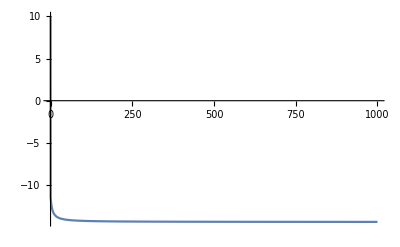

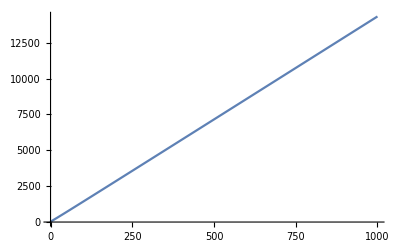

```mathematica
Plot[δx[1][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
Plot[δx[2][t]/.sols,{t,0,Subscript[t, max]},PlotRange->All]
```

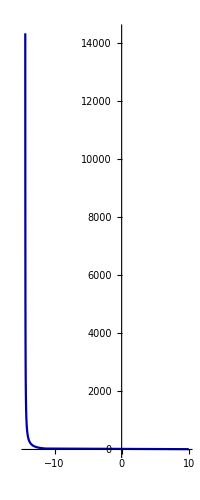

```mathematica
ParametricPlot[{δx[1][t],δx[2][t]}/.sols,{t,0,Subscript[t, max]},PlotRange->All,PlotPoints->1000,PlotStyle->Darker@Blue]
```

```mathematica
M = FullSimplify[Subscript[A, (1)]/.rates/.α->Subscript[α, c]];M//MatrixForm
```

(1/2 (-2-3 β-√(12+β (20+9 β))) | 1/2 (-2-3 β-√(12+β (20+9 β)))
1/2 (3 β+√(12+β (20+9 β))) | 1/2 (2+3 β+√(12+β (20+9 β))))

```mathematica
K = {{0,1},{1,0}};K//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
T=K.Inverse[Transpose[Eigenvectors[M]]];T//MatrixForm
```

((3 β+√(12+20 β+9 β^2))/(2 √2 √(2+3 β+√(12+20 β+9 β^2))) | (2+3 β+√(12+20 β+9 β^2)+√2 √(2+3 β+√(12+20 β+9 β^2)))/(2 √2 √(2+3 β+√(12+20 β+9 β^2)))
-(3 β+√(12+20 β+9 β^2))/(2 √2 √(2+3 β+√(12+20 β+9 β^2))) | -(2+3 β+√(12+20 β+9 β^2)-√2 √(2+3 β+√(12+20 β+9 β^2)))/(2 √2 √(2+3 β+√(12+20 β+9 β^2))))

```mathematica
T.M.Inverse[T]//FullSimplify//MatrixForm
```

((√(2+3 β+√(12+β (20+9 β))))/(√2) | 0
0 | -(√(2+3 β+√(12+β (20+9 β))))/(√2))

```mathematica
II = {{0,1},{-1,0}};II//MatrixForm
```

(0 | 1
-1 | 0)

```mathematica
U=Inverse[Transpose[Eigenvectors[II]]];U//MatrixForm
```

(ⅈ/2 | 1/2
-ⅈ/2 | 1/2)

```mathematica
U.II.Inverse[U]//FullSimplify//MatrixForm
```

(ⅈ | 0
0 | -ⅈ)

```mathematica
vecδy = Table[δy[i],{i,1,NN}]
```

{δy[1],δy[2]}

```mathematica
vecδx = Inverse[T].U.vecδy//FullSimplify/.β->(ω^2-1)
```

{(ⅈ √2 √(2+3 β+√(12+β (20+9 β))) δy[1]-(2+3 β+√(12+β (20+9 β))) δy[2])/(3 β+√(12+β (20+9 β))),δy[2]}

```mathematica
Subscript[A, δy]= FullSimplify@Subscript[A, δ]/.Table[δx[i]->vecδx[[i]],{i,1,NN}]
```

{1/(√δα)(-1-(2 √δα (ⅈ √2 √(2+3 β+√(12+β (20+9 β))) δy[1]-(2+3 β+√(12+β (20+9 β))) δy[2]))/(3 β+√(12+β (20+9 β)))+(-2-(3 β)/2-1/2 √(12+β (20+9 β))+δα) (-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δy[2])+(-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δy[2]) (1+(√δα (ⅈ √2 √(2+3 β+√(12+β (20+9 β))) δy[1]-(2+3 β+√(12+β (20+9 β))) δy[2]))/(3 β+√(12+β (20+9 β))))^2-β (1+(√δα (ⅈ √2 √(2+3 β+√(12+β (20+9 β))) δy[1]-(2+3 β+√(12+β (20+9 β))) δy[2]))/(3 β+√(12+β (20+9 β))))^3),1/(√δα)(1+(√δα (ⅈ √2 √(2+3 β+√(12+β (20+9 β))) δy[1]-(2+3 β+√(12+β (20+9 β))) δy[2]))/(3 β+√(12+β (20+9 β)))-(-2-(3 β)/2-1/2 √(12+β (20+9 β))+δα) (-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δy[2])-(-(2 (1+β))/(2+3 β+√(12+β (20+9 β))-2 δα)+√δα δy[2]) (1+(√δα (ⅈ √2 √(2+3 β+√(12+β (20+9 β))) δy[1]-(2+3 β+√(12+β (20+9 β))) δy[2]))/(3 β+√(12+β (20+9 β))))^2+β (1+(√δα (ⅈ √2 √(2+3 β+√(12+β (20+9 β))) δy[1]-(2+3 β+√(12+β (20+9 β))) δy[2]))/(3 β+√(12+β (20+9 β))))^3)}

```mathematica
V= Inverse[U].T.Subscript[A, δy]//FullSimplify
```

{1/(128 β^2 √(1+4 β (3+β)))ⅈ (4 δy[1] (48 ⅈ β^2 √(1+4 β (3+β))+32 ⅈ β^3 √(1+4 β (3+β))-(1+2 β) (1+4 β (3+β)) (5 β-δα) √δα δy[1])-64 β^2 (1+4 β (3+β)) δy[2]-4 (-1+4 β^2) δα^(3/2) δy[2] (-2 ⅈ √(1+4 β (3+β)) δy[1]+(-1+2 β) δy[2])+4 β (1+2 β) √δα δy[2] (-2 ⅈ (3+10 β) √(1+4 β (3+β)) δy[1]+(-1+2 β) (11+10 β) δy[2])+4 (1+2 β) √δα {}⟦1⟧⟦1,2⟧ ((1+4 β (3+β)) δy[1]^2+2 ⅈ (-1+2 β) √(1+4 β (3+β)) δy[1] δy[2]-(1-2 β)^2 δy[2]^2)+2 (1+2 β) δα (-ⅈ (1+4 β (3+β))^(3/2) δy[1]^3+(1+6 β) (1+4 β (3+β)) δy[1]^2 δy[2]+ⅈ (-1+2 β) (5+6 β) √(1+4 β (3+β)) δy[1] δy[2]^2-(1-2 β)^2 (3+2 β) δy[2]^3)),1/(64 β^2)(32 β^2 (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])+2 √δα (5 β-δα-{}⟦1⟧⟦1,2⟧) (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])^2+δα (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])^3-4 δy[2] (32 β^2+8 β √δα (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])+δα (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])^2))}

```mathematica
O1 = FullSimplify@Series[V,{δα,0,1}]
```

{(-1/2 (3+2 β) δy[1]-1/2 ⅈ √(1+4 β (3+β)) δy[2])+1/(32 β^2 √(1+4 β (3+β)))ⅈ (1+2 β) (-5 β (1+4 β (3+β)) δy[1]^2+β δy[2] (-2 ⅈ (3+10 β) √(1+4 β (3+β)) δy[1]+(-1+2 β) (11+10 β) δy[2])+{}⟦1⟧⟦1,2⟧ ((1+4 β (3+β)) δy[1]^2+2 ⅈ (-1+2 β) √(1+4 β (3+β)) δy[1] δy[2]-(1-2 β)^2 δy[2]^2)) √δα+1/(64 β^2 √(1+4 β (3+β)))ⅈ (1+2 β) (-ⅈ (1+4 β (3+β))^(3/2) δy[1]^3+(1+6 β) (1+4 β (3+β)) δy[1]^2 δy[2]+ⅈ (-1+2 β) (5+6 β) √(1+4 β (3+β)) δy[1] δy[2]^2-(1-2 β)^2 (3+2 β) δy[2]^3) δα+O[δα]^(3/2),1/2 (ⅈ √(1+4 β (3+β)) δy[1]-(3+2 β) δy[2])+((-32 β δy[2] (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])+2 (5 β-{}⟦1⟧⟦1,2⟧) (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])^2) √δα)/(64 β^2)+((√(1+4 β (3+β)) δy[1]+ⅈ (-1+2 β) δy[2])^2 (-ⅈ √(1+4 β (3+β)) δy[1]+(3+2 β) δy[2]) δα)/(64 β^2)+O[δα]^(3/2)}

```mathematica
Subscript[F, 0]=Coefficient[O1,δα,1/2]
```

{1/(32 β^2 √(1+4 β (3+β)))ⅈ (1+2 β) (-5 β (1+4 β (3+β)) δy[1]^2+β δy[2] (-2 ⅈ (3+10 β) √(1+4 β (3+β)) δy[1]+(-1+2 β) (11+10 β) δy[2])+{}⟦1⟧⟦1,2⟧ ((1+4 β (3+β)) δy[1]^2+2 ⅈ (-1+2 β) √(1+4 β (3+β)) δy[1] δy[2]-(1-2 β)^2 δy[2]^2)),(-32 β δy[2] (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])+2 (5 β-{}⟦1⟧⟦1,2⟧) (ⅈ √(1+4 β (3+β)) δy[1]+δy[2]-2 β δy[2])^2)/(64 β^2)}